```mathematica
k Q
−1
(2 k−2 i)
i=0
```

0.288788095086602

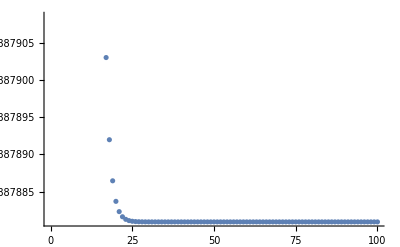

```mathematica
list=N[∏_(i=0)^(#-1) (2^#-2^i)]/(2^(#^2))&/@Range[100];
list[[80]]
ListPlot[list]
```

{0.502664,0.377958,0.328537,0.308299,0.299383,0.293496,0.295491,0.284787,0.296138,0.283126,0.287952,0.294568,0.283302,0.291886,0.288052,0.28885,0.289436,0.284625,0.284495,0.286664}

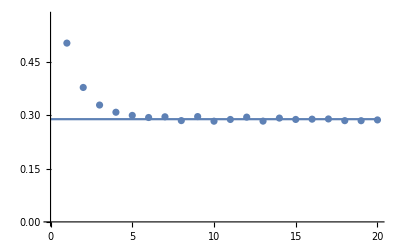

```mathematica
max=20;
f[n_]:=1/N[Mean[nahodnaRegularniMatice[n]⟦2⟧&/@Range[5000]]]
l=f[#]&/@Range[max]
Show[
Plot[list[[80]],{x,0,max}],
ListPlot[l]
]
```